```mathematica
以下是束缚态的边值计算
```

```mathematica
方势阱的偶束缚态
```

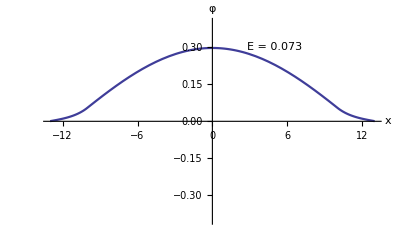

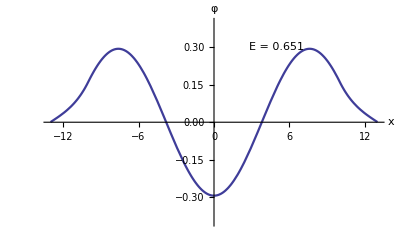

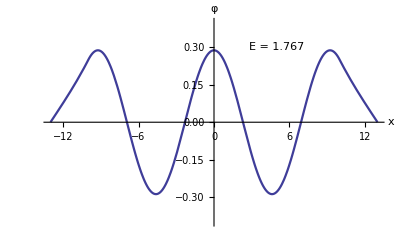

```mathematica
(*searching for even states*)
a=10.0;V0=2.0;coef=0.262116;
V[x_]:=If[Abs[x]<a,0,V0];
x1=-1.3a;x2=1.3a;δ=10^-4;ϵ=0.001;
Do[
s=NDSolve[{ψ''[x]-coef*(V[x]-energy)*ψ[x]==0,
ψ[x1]==δ,ψ[x2]==δ},ψ,{x,x1,x2}];
ϕ[x_]:=(ψ[x]/.s[[1]])^2;
int=NIntegrate[ϕ[x],{x,x1,x2},
MaxRecursion->20];
φ[x_]:=(ψ[x]/.s[[1]])/√int;
If[(ϕ'[x1]>0)&&(ϕ'[x2]<0)&&(Abs[φ[x1]]<ϵ),
g=Plot[φ[x],{x,x1,x2},AxesLabel->{"x","φ"},
PlotRange->0.4,BaseStyle->{FontSize->13},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
Epilog->Text["E = "<>ToString[energy],
{0.5a,0.3}]];Print[g]],
{energy,0.01,V0,0.001}]
Clear[coef,x1,x2,s,int,ψ,ϕ,φ,δ,ϵ,z]
```

```mathematica
方势阱的奇束缚态
```

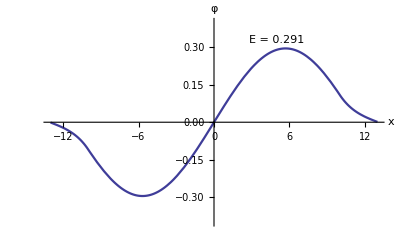

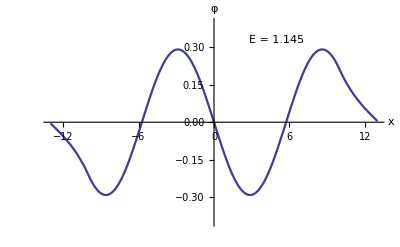

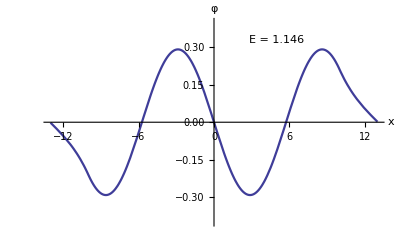

```mathematica
(*searching for odd states*)
a=10.0;V0=2.0;coef=0.262116;
V[x_]:=If[Abs[x]<a,0,V0];
x1=-1.3a;x2=1.3a;δ=10^-4;ϵ=0.005;
Do[
s=NDSolve[{ψ''[x]-coef*(V[x]-energy)*ψ[x]==0,
ψ[x1]==-δ,ψ[x2]==δ},ψ,{x,x1,x2}];
ϕ[x_]:=(ψ[x]/.s[[1]])^2;
int=NIntegrate[ϕ[x],{x,x1,x2},MaxRecursion->20];
φ[x_]:=(ψ[x]/.s[[1]])/√int;
If[(ϕ'[x1]>0)&&(ϕ'[x2]<0)&&(Abs[φ[x1]]<ϵ),
g=Plot[φ[x],{x,x1,x2},AxesLabel->{"x","φ"},
PlotRange->0.4,BaseStyle->{FontSize->13},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
Epilog->Text["E = "<>ToString[energy],
{0.5a,0.33}]];Print[g]],
{energy,0.01,V0,0.001}]
Clear[coef,x1,x2,s,int,ψ,ϕ,φ,V]
```

```mathematica
另一个例子
```

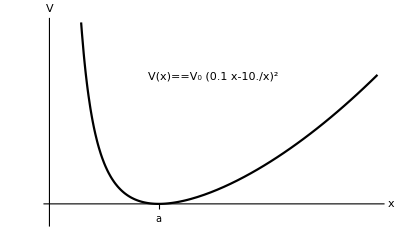

```mathematica
V01=1;a1=1;
V1[x_]:=V01 (x/a1-a1/x)^2
Plot[V1[x],{x,0.01,3a1},PlotRange->{-1,10},PlotStyle->{Black,Thickness[0.004]},AxesStyle->Thickness[0.003],Ticks->{{{a1,"a"}},None},BaseStyle->{FontSize->14},AxesLabel->{"x","V"},Epilog->Text[V[x]==Subscript[V, 0](x/a-a/x)^2,{1.5a1,7}]]
Clear[V0,V,a]
```

x1 = 0.45685, x2 = 2.1889

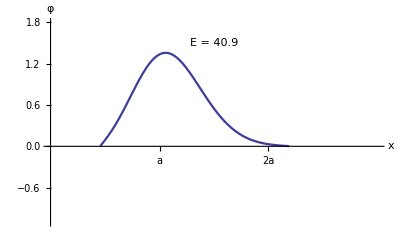

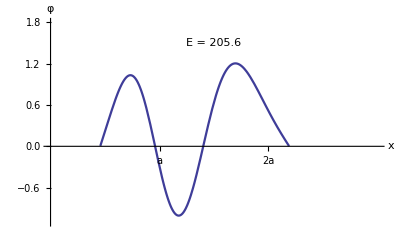

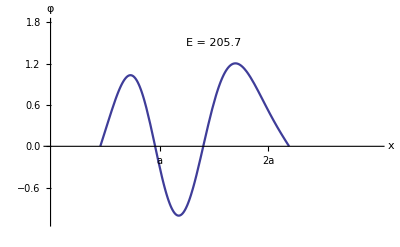

```mathematica
(*searching for even states*)
a=1.0;V0=100.0;coef=0.262116;
V[x_]:=V0*(a/x-x/a)^2;m=3;
s=Solve[V[x]==m*V0,x];s=x/.s;
s=Select[s,#>0&];
x1=Min[s];x2=Max[s];
Print["x1 = ",x1,", ","x2 = ",x2];
δ=10^-4;ϵ=0.01;
Do[
s=NDSolve[{ψ''[x]-coef*(V[x]-energy)*ψ[x]==0,
ψ[x1]==2δ,ψ[x2]==δ},ψ,{x,x1,x2}];
ϕ[x_]:=(ψ[x]/.s[[1]])^2;
int=NIntegrate[ϕ[x],{x,x1,x2},MaxRecursion->20];
φ[x_]:=(ψ[x]/.s[[1]])/√int;
If[(ϕ'[x1]>0)&&(ϕ'[x2]<0)&&(Abs[φ[x1]]<ϵ),
g=Plot[φ[x],{x,x1,x2},AxesLabel->{"x","φ"},
PlotRange->{{0,3a},{-1.1,1.8}},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],AxesOrigin->{0,0},
BaseStyle->{FontSize->14},
Ticks->{{{a,"a"},{2a,"2a"}},Automatic},
Epilog->Text["E = "<>ToString[energy],
{1.5a,1.5}]];Print[g]],
{energy,1,m V0,0.1}]
Clear[V,m,coef,x1,x2,s,int,ψ,ϕ,φ,δ,ϵ,z]
Beep[];
```

x1 = 0.381966, x2 = 2.61803

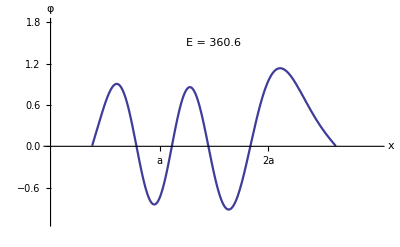

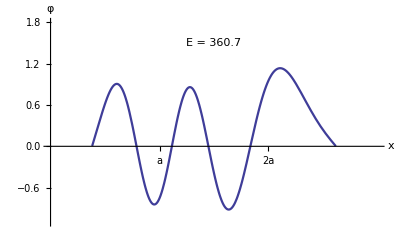

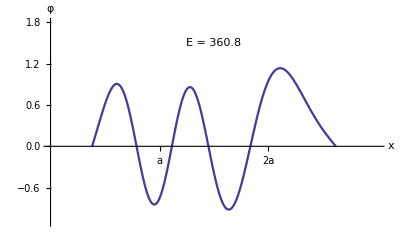

```mathematica
(*searching for even states*)
a=1.0;V0=100.0;coef=0.262116;
V[x_]:=V0*(a/x-x/a)^2;m=5;
s=Solve[V[x]==m*V0,x];s=x/.s;
s=Select[s,#>0&];
x1=Min[s];x2=Max[s];
Print["x1 = ",x1,", ","x2 = ",x2];
δ=10^-4;ϵ=0.01;
Do[
s=NDSolve[{ψ''[x]-coef*(V[x]-energy)*ψ[x]==0,
ψ[x1]==2δ,ψ[x2]==δ},ψ,{x,x1,x2}];
ϕ[x_]:=(ψ[x]/.s[[1]])^2;
int=NIntegrate[ϕ[x],{x,x1,x2},MaxRecursion->20];
φ[x_]:=(ψ[x]/.s[[1]])/√int;
If[(ϕ'[x1]>0)&&(ϕ'[x2]<0)&&(Abs[φ[x1]]<ϵ),
g=Plot[φ[x],{x,x1,x2},AxesLabel->{"x","φ"},
PlotRange->{{0,3.0a},{-1.1,1.8}},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],AxesOrigin->{0,0},
BaseStyle->{FontSize->13},
Ticks->{{{a,"a"},{2a,"2a"}},Automatic},
Epilog->Text["E = "<>ToString[energy],
{1.5a,1.5}]];Print[g]],
{energy,3V0,m V0,0.1}]
Clear[V,m,coef,x1,x2,s,int,ψ,ϕ,φ,δ,ϵ,z]
Beep[];
```

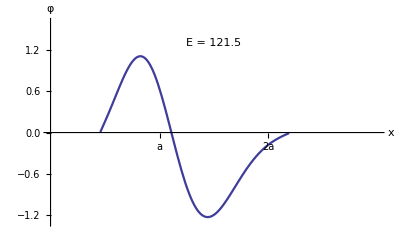

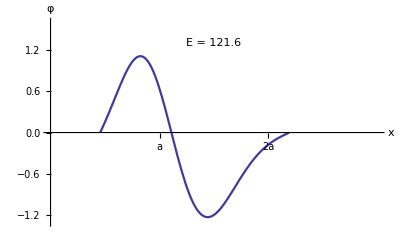

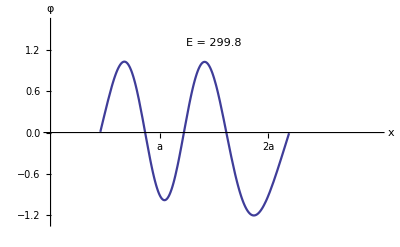

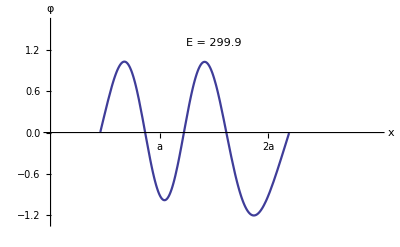

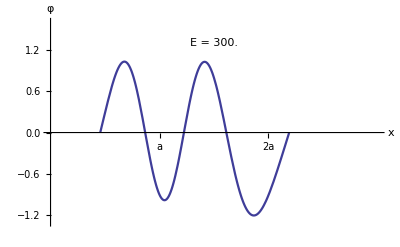

```mathematica
(*searching for odd states*)
a=1.0;V0=100.0;coef=0.262116;
V[x_]:=V0*(a/x-x/a)^2;m=3;
s=Solve[V[x]==m*V0,x];s=x/.s;
s=Select[s,#>0&];
x1=Min[s];x2=Max[s];δ=10^-4;ϵ=0.01;
Do[
s=NDSolve[{ψ''[x]-coef*(V[x]-energy)*ψ[x]==0,
ψ[x1]==δ,ψ[x2]==-δ},ψ,{x,x1,x2}];
ϕ[x_]:=(ψ[x]/.s[[1]])^2;
int=NIntegrate[ϕ[x],{x,x1,x2},MaxRecursion->20];
φ[x_]:=(ψ[x]/.s[[1]])/√int;
If[(ϕ'[x1]>0)&&(ϕ'[x2]<0)&&(Abs[φ[x1]]<ϵ),
g=Plot[φ[x],{x,x1,x2},AxesLabel->{"x","φ"},
PlotRange->{{0,3.0a},{-1.3,1.6}},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],AxesOrigin->{0,0},
BaseStyle->{FontSize->13},
Ticks->{{{a,"a"},{2a,"2a"}},Automatic},
Epilog->Text["E = "<>ToString[energy],
{1.5a,1.3}]];Print[g]],
{energy,100,m V0,0.1}]
Clear[V,m,coef,x1,x2,s,int,ψ,ϕ,φ,δ,ϵ,z]
Beep[];
```

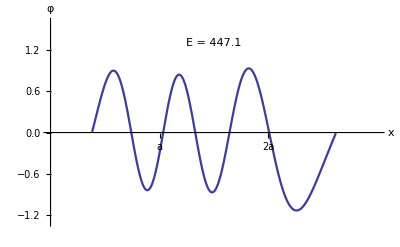

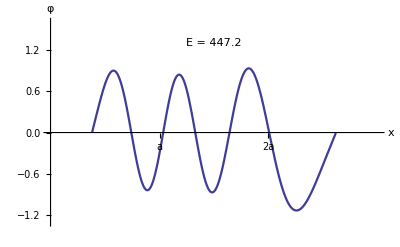

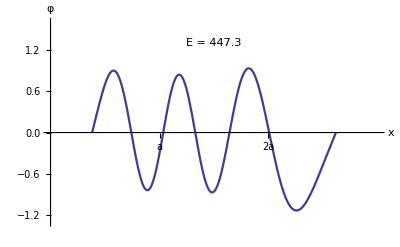

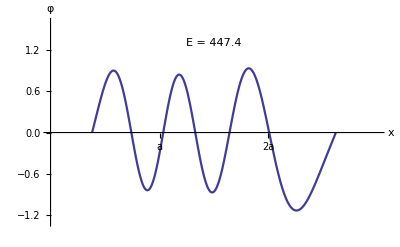

```mathematica
(*searching for odd states*)
a=1.0;V0=100.0;coef=0.262116;
V[x_]:=V0*(a/x-x/a)^2;m=5;
s=Solve[V[x]==m*V0,x];s=x/.s;
s=Select[s,#>0&];
x1=Min[s];x2=Max[s];δ=10^-4;ϵ=0.01;
Do[
s=NDSolve[{ψ''[x]-coef*(V[x]-energy)*ψ[x]==0,
ψ[x1]==δ,ψ[x2]==-δ},ψ,{x,x1,x2},
MaxSteps->∞];ϕ[x_]:=(ψ[x]/.s[[1]])^2;
int=NIntegrate[ϕ[x],{x,x1,x2},MaxRecursion->20];
φ[x_]:=(ψ[x]/.s[[1]])/√int;
If[(ϕ'[x1]>0)&&(ϕ'[x2]<0)&&(Abs[φ[x1]]<ϵ),
g=Plot[φ[x],{x,x1,x2},AxesLabel->{"x","φ"},
PlotRange->{{0,3.0a},{-1.3,1.6}},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],AxesOrigin->{0,0},
BaseStyle->{FontSize->13},
Ticks->{{{a,"a"},{2a,"2a"}},Automatic},
Epilog->Text["E = "<>ToString[energy],
{1.5a,1.3}]];Print[g]],
{energy,3V0,m V0,0.1}]
Clear[V,m,coef,x1,x2,s,int,ψ,ϕ,φ,δ,ϵ,z]
Beep[];
```

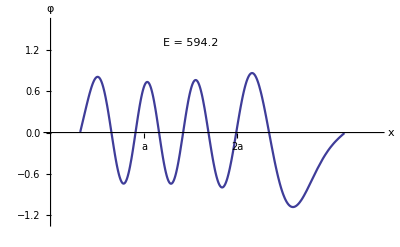

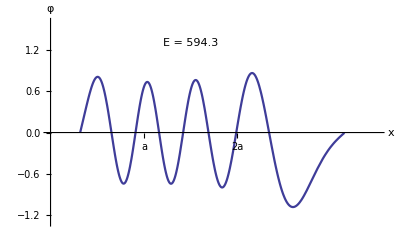

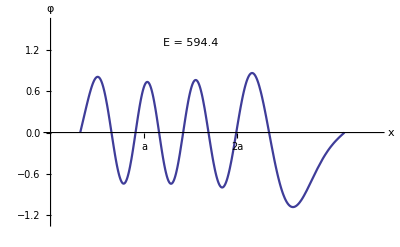

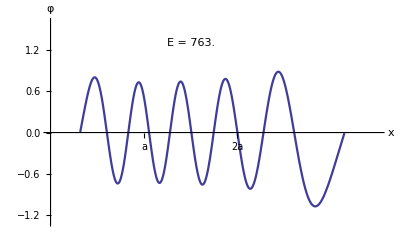

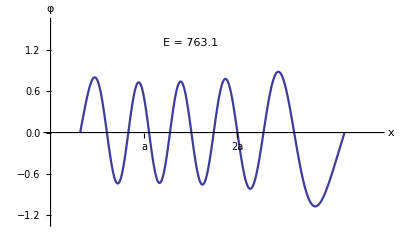

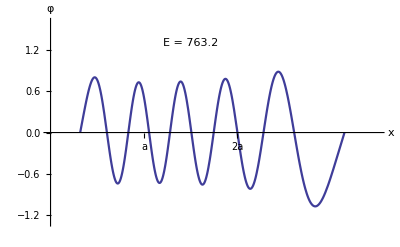

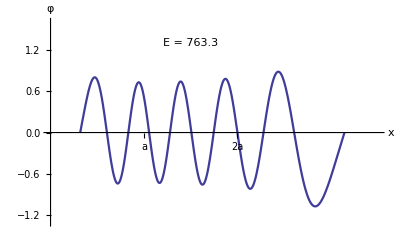

```mathematica
(*searching for odd states*)
a=1.0;V0=100.0;coef=0.262116;
V[x_]:=V0*(a/x-x/a)^2;m=8;
s=Solve[V[x]==m*V0,x];s=x/.s;
s=Select[s,#>0&];
x1=Min[s];x2=Max[s];δ=10^-4;ϵ=0.01;
Do[
s=NDSolve[{ψ''[x]-coef*(V[x]-energy)*ψ[x]==0,
ψ[x1]==δ,ψ[x2]==-δ},ψ,{x,x1,x2},
MaxSteps->∞];ϕ[x_]:=(ψ[x]/.s[[1]])^2;
int=NIntegrate[ϕ[x],{x,x1,x2},MaxRecursion->20];
φ[x_]:=(ψ[x]/.s[[1]])/√int;
If[(ϕ'[x1]>0)&&(ϕ'[x2]<0)&&(Abs[φ[x1]]<ϵ),
g=Plot[φ[x],{x,x1,x2},AxesLabel->{"x","φ"},
PlotRange->{{0,3.5a},{-1.3,1.6}},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],AxesOrigin->{0,0},
BaseStyle->{FontSize->13},
Ticks->{{{a,"a"},{2a,"2a"}},Automatic},
Epilog->Text["E = "<>ToString[energy],
{1.5a,1.3}]];Print[g]],
{energy,5V0,m V0,0.1}]
Clear[V,m,coef,x1,x2,s,int,ψ,ϕ,φ,δ,ϵ,z]
Beep[];
```

```mathematica
先看能量分布
```

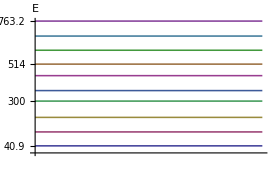

```mathematica
energy={40.9,121.5,205.7,300,360.8,447.3,
514,594.4,676.5,763.2};
Plot[Evaluate[energy],{x,0,1},AxesLabel->"E",
Ticks->{None,energy},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[energy]
```

```mathematica
寻找285左右的态
```

```mathematica
求解范围的新设定
```

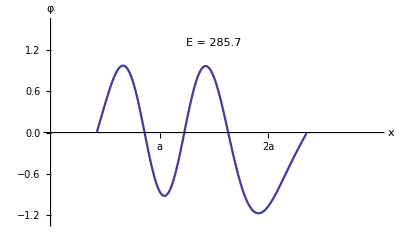

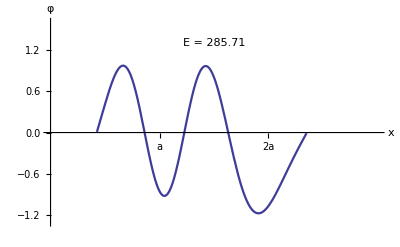

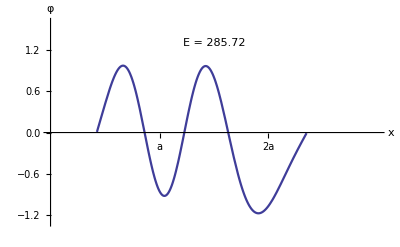

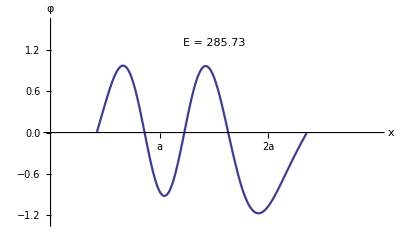

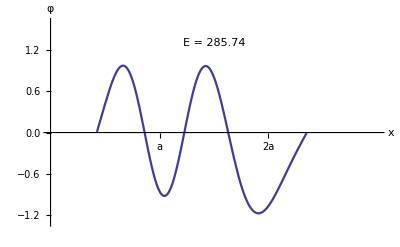

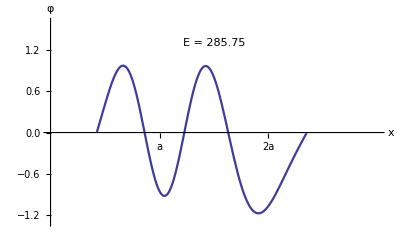

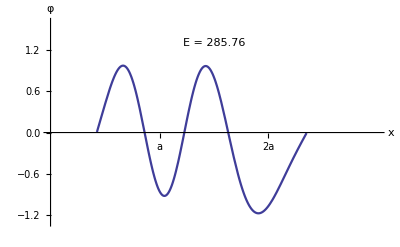

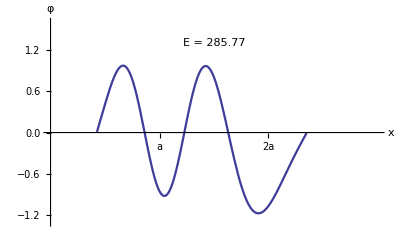

```mathematica
(*searching for odd states*)
a=1.0;V0=100.0;coef=0.262116;
V[x_]:=V0*(a/x-x/a)^2;m=3.7;
s=Solve[V[x]==m*V0,x];s=x/.s;
s=Select[s,#>0&];
x1=Min[s];x2=Max[s];δ=10^-5;ϵ=0.01;
Do[
s=NDSolve[{ψ''[x]-coef*(V[x]-energy)*ψ[x]==0,
ψ[x1]==δ,ψ[x2]==-δ},ψ,{x,x1,x2}];
ϕ[x_]:=(ψ[x]/.s[[1]])^2;
int=NIntegrate[ϕ[x],{x,x1,x2},MaxRecursion->20];
φ[x_]:=(ψ[x]/.s[[1]])/√int;
If[(ϕ'[x1]>0)&&(ϕ'[x2]<0)&&(Abs[φ[x1]]<ϵ),
g=Plot[φ[x],{x,x1,x2},AxesLabel->{"x","φ"},
PlotRange->{{0,3.0a},{-1.3,1.6}},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],AxesOrigin->{0,0},
BaseStyle->{FontSize->13},
Ticks->{{{a,"a"},{2a,"2a"}},Automatic},
Epilog->Text["E = "<>ToString[energy],
{1.5a,1.3}]];Print[g]],
{energy,280,290,0.01}]
Clear[V,m,coef,x1,x2,s,int,ψ,ϕ,φ,δ,ϵ,z]
Beep[];
```

```mathematica
能级的理论值分布
```

```mathematica
Partition[Table[40.0+78.08 i,{i,0,9}],5]//
TableForm
```

40. | 118.08 | 196.16 | 274.24 | 352.32
430.4 | 508.48 | 586.56 | 664.64 | 742.72

```mathematica
寻找与理论接近的态,改变计算的边界
```

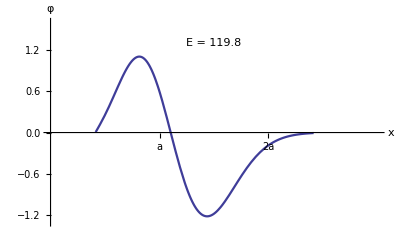

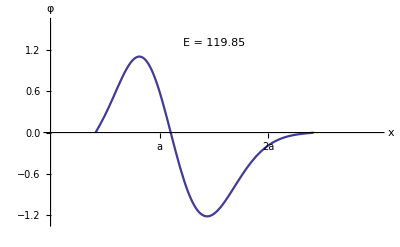

```mathematica
a=1.0;V0=100.0;coef=0.262116;
V[x_]:=V0*(a/x-x/a)^2;m=5.7;
s=Solve[V[x]==4*V0,x];s=x/.s;
s=Select[s,#>0&];
x1=Min[s];x2=Max[s];δ=10^-4;ϵ=0.01;
Do[
s=NDSolve[{ψ''[x]-coef*(V[x]-energy)*ψ[x]==0,
ψ[x1]==δ,ψ[x2]==-δ},ψ,{x,x1,x2}];
ϕ[x_]:=(ψ[x]/.s[[1]])^2;
int=NIntegrate[ϕ[x],{x,x1,x2},MaxRecursion->20];
φ[x_]:=(ψ[x]/.s[[1]])/√int;
If[(ϕ'[x1]>0)&&(ϕ'[x2]<0)&&(Abs[φ[x1]]<ϵ),
g=Plot[φ[x],{x,x1,x2},AxesLabel->{"x","φ"},
PlotRange->{{0,3.0a},{-1.3,1.6}},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],AxesOrigin->{0,0},
BaseStyle->{FontSize->13},
Ticks->{{{a,"a"},{2a,"2a"}},Automatic},
Epilog->Text["E = "<>ToString[energy],
{1.5a,1.3}]];Print[g]],{energy,115,125,0.05}]
Clear[V,m,coef,x1,x2,s,int,ψ,ϕ,φ,δ,ϵ,z]
Beep[];
```